```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
g1=Show[Graphics3D[{Opacity[0.2],LightGray,Cone[{{0,0,0},{0,0,1}}]},Axes->True,Ticks->False,PlotRange->{{-1,1},{-1,1},{0,1}},Boxed->False,AxesStyle->Black,AxesLabel->{"θ_1","θ_2","q"},LabelStyle->{Black,FontSize->16},AxesOrigin->{-1,1,0}],ParametricPlot3D[{0.5 Sin[u],0.5 Cos[u],0.5},{u,0,2Pi},PlotStyle->Directive[Thickness[0.01],Darker@Blue],PlotPoints->2000],ParametricPlot3D[{0.75 Sin[u],0.75 Cos[u],0.25},{u,0,2Pi},PlotStyle->Directive[Lighter@Blue,Thickness[0.01]],PlotPoints->2000],ParametricPlot3D[{ 0.99Sin[u],0.99Cos[u],0.02},{u,0,2Pi},PlotStyle->Directive[LightBlue,Thickness[0.01]],PlotPoints->2000],Graphics3D[{Darker@Darker@Darker@Blue,PointSize[0.02],Point[{0,0,1}]}],ViewPoint->{0.4048327584826207,-3.225001578709785,0.940996947380142},ViewVertical->{0.060356490303168836,-0.3385968794638712,1.8779874837661858}]
```

-Graphics3D-

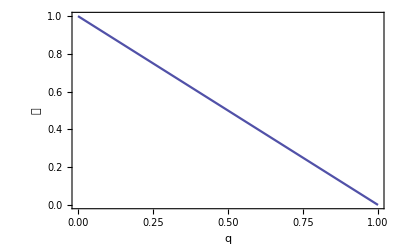

```mathematica
g2=Plot[1-q,{q,0,1},PlotStyle->Gray,Frame->{True,True,False,False},FrameTicks->None,FrameLabel->{"q","𝒱"},LabelStyle->{Black,FontSize->16},ColorFunction->"DeepSeaColors"]
```

```mathematica
gFinal=GraphicsRow[{g1,g2},ImageSize->800]
```

-Graphics-

```mathematica
Export["../figures/contour_volumes_reduxa.png",gFinal,ImageResolution->400]
```

../figures/contour_volumes_redux.png

## Check that my assertions about contour volumes are true

```mathematica
fQ[x_,y_]:=Sqrt[x^2+y^2]
```

```mathematica
fSampleCircle[]:=Block[{proposed=RandomVariate[UniformDistribution[{-1,1}],2]},If[proposed[[1]]^2+proposed[[2]]^2≤ 1,proposed,fSampleCircle[]]]
```

```mathematica
lsamples=Table[fSampleCircle[],100000];
lQ=fQ@@@lsamples;
```

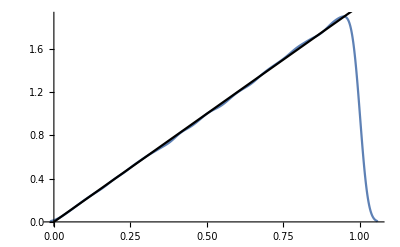

```mathematica
Show[SmoothHistogram[lQ],Plot[2x,{x,0,1},PlotStyle->Black]]
```